# Call Python to compute CY metrics

Getting started
The easiest thing to get started would be to just run the entire notebook.

Documentation
• To see all functions currently available run ?cymetric
• If you want to see detailed documentation for any of the functions (including its input, options, output, examples), run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values. 
• The value of all global options can be checked with GetGlobalOptions[]

Setting up the program
In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and (older versions of) Mathematica, setup will automatically apply a bug fix. The program will create a text file (with the same name as the notebook, with an extension “.m”, at the same location as the notebook file) that stores some options, e.g. the location of the virtual environment to use for future runs.
More advanced (if you do not want to just call Setup[] and be done with it):
1.) If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package from the web.
You can also download the package file and copy it to Mathematica’s Application folder. 
To find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/ruehlef/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and load it with  <<cymetric`

```mathematica
Quit[]
```

```mathematica
Get["https://raw.githubusercontent.com/ruehlef/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where the virtual environment for python will be created. Defaults to the User's Home Directory*)
PathToVenv=FileNameJoin[{$HomeDirectory,"venv-mathematica"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

Mathematica discovered the following Python environments on your system:

Looking for Python

Found Python version 3.9.22 at /opt/homebrew/bin/python3.9.

Creating virtual environment at /Users/ruehle/venv-mathematica

Upgrading pip, wheel, setuptools...

Installing h5py...

Installing joblib...

Installing numpy...

Installing pyyaml...

Installing pyzmq...

Installing scipy...

Installing sympy...

Installing wolframclient...

Installing cymetric...

Registering venv with mathematica...

Checking whether 'externalevaluate.py' needs to be patched for this version...

Testing new environment...

Everything is working!

/opt/homebrew/Cellar/python@3.9/3.9.22/Frameworks/Python.framework/Versions/3.9/lib/python3.9/importlib/__init__.py:127: UserWarning: pkg_resources is deprecated as an API. See https://setuptools.pypa.io/en/latest/pkg_resources.html. The pkg_resources package is slated for removal as early as 2025-11-30. Refrain from using this package or pin to Setuptools<81.

return _bootstrap._gcd_import(name[level:], package, level)

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000}

Now we generate some points. We set the output Directory to “Quintic”

```mathematica
??GeneratePoints
```

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
ChangeSetting["Dir",outDir];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+0 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
pdim={4};kmod={1};
```

```mathematica
res=GeneratePoints[poly,pdim,"Points"->100000,"KahlerModuli"->kmod];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Generating 100000 points...

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /Users/ruehle/Desktop/test_package/notebooks/Quintic/points.pickle

Now we train the NN. We choose the PhiFS model here. (Training can be made faster if one sets “EvaluateModel”->False). 
We also set Verbose to 3 to see some more info during the training process.

```mathematica
history=TrainNN["Epochs"->10,"EvaluateModel"->True,"Verbose"->3];
```

DEBUG:mathematica:{'ActivationFunctions': array(['gelu', 'gelu', 'gelu'], dtype='<U4'), 'Alphas': array([1., 1., 1., 1., 1.]), 'BatchSizes': array([   64, 50000]), 'Dir': '/Users/ruehle/Desktop/test_package/notebooks/Quintic', 'DisableGPU': False, 'HiddenLayers': array([64, 64, 64]), 'LearningRate': 0.001, 'Model': 'PhiFS', 'Precision': 10, 'PrintLosses': array([ True,  True,  True,  True,  True]), 'PrintMeasures': array([ True,  True,  True,  True,  True]), 'Python': '/Users/ruehle/venv-mathematica/bin/python', 'Verbose': 3, 'Epochs': 10, 'EvaluateModel': True, 'logger_level': 10}

DEBUG:mathematica:Using tensorflow framework

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Using model PhiFS

DEBUG:mathematica:Model: "sequential"

┏━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━┳━━━━━━━━━━━━━━━━━━━━━━━━┳━━━━━━━━━━━━━━━┓

┃ Layer (type)                    ┃ Output Shape           ┃       Param # ┃

┡━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━━╇━━━━━━━━━━━━━━━━━━━━━━━━╇━━━━━━━━━━━━━━━┩

│ dense (Dense)                   │ (None, 64)             │           704 │

├─────────────────────────────────┼────────────────────────┼───────────────┤

│ dense_1 (Dense)                 │ (None, 64)             │         4,160 │

├─────────────────────────────────┼────────────────────────┼───────────────┤

│ dense_2 (Dense)                 │ (None, 64)             │         4,160 │

├─────────────────────────────────┼────────────────────────┼───────────────┤

│ dense_3 (Dense)                 │ (None, 1)              │            64 │

└─────────────────────────────────┴────────────────────────┴───────────────┘

Total params: 9,088 (35.50 KB)

Trainable params: 9,088 (35.50 KB)

Non-trainable params: 0 (0.00 B)

Epoch  1/10

1407/1407 - 5s - 4ms/step - kaehler_loss: 0.0000e+00 - loss: 0.2028 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1996 - transition_loss: 0.0032 - volk_loss: 0.0000e+00

- Sigma measure val:      0.1640

- Transition measure val: 0.0032

- Ricci measure val:      1.3075

- Volk val:               4.8340

2/2 - 6s - 3s/step - kaehler_loss: 0.0000e+00 - loss: 0.1625 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1593 - transition_loss: 0.0032 - volk_loss: 0.0000e+00 - sigma_val: 0.1640 - transition_val: 0.0032 - ricci_val: 1.3075 - volk_val: 4.8340

Epoch  2/10

1407/1407 - 4s - 3ms/step - kaehler_loss: 0.0000e+00 - loss: 0.1801 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1786 - transition_loss: 0.0015 - volk_loss: 0.0000e+00

- Sigma measure val:      0.1582

- Transition measure val: 0.0026

- Ricci measure val:      1.1216

- Volk val:               4.9448

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.1690 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1660 - transition_loss: 0.0030 - volk_loss: 0.0000e+00 - sigma_val: 0.1582 - transition_val: 0.0026 - ricci_val: 1.1216 - volk_val: 4.9448

Epoch  3/10

1407/1407 - 4s - 3ms/step - kaehler_loss: 0.0000e+00 - loss: 0.1718 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1699 - transition_loss: 0.0019 - volk_loss: 0.0000e+00

- Sigma measure val:      0.1478

- Transition measure val: 0.0020

- Ricci measure val:      1.0525

- Volk val:               4.6686

2/2 - 4s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.1515 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1495 - transition_loss: 0.0020 - volk_loss: 0.0000e+00 - sigma_val: 0.1478 - transition_val: 0.0020 - ricci_val: 1.0525 - volk_val: 4.6686

Epoch  4/10

1407/1407 - 3s - 2ms/step - kaehler_loss: 0.0000e+00 - loss: 0.1518 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1493 - transition_loss: 0.0025 - volk_loss: 0.0000e+00

- Sigma measure val:      0.1309

- Transition measure val: 0.0027

- Ricci measure val:      0.9142

- Volk val:               5.0575

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.1368 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1340 - transition_loss: 0.0028 - volk_loss: 0.0000e+00 - sigma_val: 0.1309 - transition_val: 0.0027 - ricci_val: 0.9142 - volk_val: 5.0575

Epoch  5/10

1407/1407 - 3s - 2ms/step - kaehler_loss: 0.0000e+00 - loss: 0.0785 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0751 - transition_loss: 0.0035 - volk_loss: 0.0000e+00

- Sigma measure val:      0.1021

- Transition measure val: 0.0035

- Ricci measure val:      0.5435

- Volk val:               4.8445

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.1033 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0999 - transition_loss: 0.0035 - volk_loss: 0.0000e+00 - sigma_val: 0.1021 - transition_val: 0.0035 - ricci_val: 0.5435 - volk_val: 4.8445

Epoch  6/10

1407/1407 - 4s - 3ms/step - kaehler_loss: 0.0000e+00 - loss: 0.1062 - ricci_loss: 0.0000e+00 - sigma_loss: 0.1036 - transition_loss: 0.0025 - volk_loss: 0.0000e+00

- Sigma measure val:      0.0669

- Transition measure val: 0.0033

- Ricci measure val:      0.3104

- Volk val:               4.9316

2/2 - 4s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.0705 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0672 - transition_loss: 0.0033 - volk_loss: 0.0000e+00 - sigma_val: 0.0669 - transition_val: 0.0033 - ricci_val: 0.3104 - volk_val: 4.9316

Epoch  7/10

1407/1407 - 3s - 2ms/step - kaehler_loss: 0.0000e+00 - loss: 0.0482 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0459 - transition_loss: 0.0023 - volk_loss: 0.0000e+00

- Sigma measure val:      0.0519

- Transition measure val: 0.0027

- Ricci measure val:      0.2304

- Volk val:               5.0107

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.0558 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0532 - transition_loss: 0.0027 - volk_loss: 0.0000e+00 - sigma_val: 0.0519 - transition_val: 0.0027 - ricci_val: 0.2304 - volk_val: 5.0107

Epoch  8/10

1407/1407 - 4s - 3ms/step - kaehler_loss: 0.0000e+00 - loss: 0.0398 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0384 - transition_loss: 0.0013 - volk_loss: 0.0000e+00

- Sigma measure val:      0.0390

- Transition measure val: 0.0022

- Ricci measure val:      0.1797

- Volk val:               5.0374

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.0419 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0398 - transition_loss: 0.0021 - volk_loss: 0.0000e+00 - sigma_val: 0.0390 - transition_val: 0.0022 - ricci_val: 0.1797 - volk_val: 5.0374

Epoch  9/10

1407/1407 - 4s - 3ms/step - kaehler_loss: 0.0000e+00 - loss: 0.0508 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0490 - transition_loss: 0.0018 - volk_loss: 0.0000e+00

- Sigma measure val:      0.0385

- Transition measure val: 0.0017

- Ricci measure val:      0.1474

- Volk val:               5.0518

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.0426 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0409 - transition_loss: 0.0017 - volk_loss: 0.0000e+00 - sigma_val: 0.0385 - transition_val: 0.0017 - ricci_val: 0.1474 - volk_val: 5.0518

Epoch 10/10

1407/1407 - 3s - 2ms/step - kaehler_loss: 0.0000e+00 - loss: 0.0407 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0395 - transition_loss: 0.0012 - volk_loss: 0.0000e+00

- Sigma measure val:      0.0307

- Transition measure val: 0.0013

- Ricci measure val:      0.1256

- Volk val:               4.9772

2/2 - 3s - 2s/step - kaehler_loss: 0.0000e+00 - loss: 0.0324 - ricci_loss: 0.0000e+00 - sigma_loss: 0.0311 - transition_loss: 0.0013 - volk_loss: 0.0000e+00 - sigma_val: 0.0307 - transition_val: 0.0013 - ricci_val: 0.1256 - volk_val: 4.9772

DEBUG:mathematica:Saving model to: /Users/ruehle/Desktop/test_package/notebooks/Quintic/model.keras

DEBUG:mathematica:Directory exists: True

Writing training information to /Users/ruehle/Desktop/test_package/notebooks/Quintic/training_history_mathematica.m

We can access the generated points easily

```mathematica
pts=GetPoints["all"];
pts[[1]]
```

{-0.796503+0.16197 ⅈ,-0.655446+0.654241 ⅈ,0.866981+0.493746 ⅈ,1.,-0.164467-0.876786 ⅈ}

We can access the weights of the points with respect to the auxiliary measure and the trained CY metric. 
The distribution should become peaked for the CY metric around a single value, since J^3 and Ω^2 are proportional.

```mathematica
weights=GetWeights["all"];
weightsCY=GetCYWeights["all"];
```

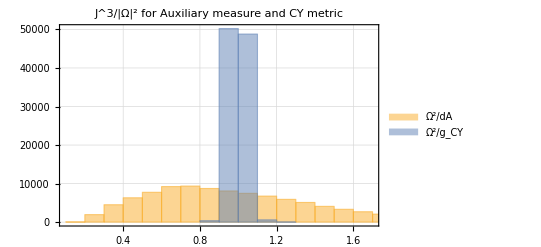

```mathematica
Histogram[{weights/Mean[weights],weightsCY/Mean[weightsCY]},PlotLabel->"J^3/|Ω|^2 for Auxiliary measure and CY metric",PlotTheme->"Detailed",ChartLegends->{ "Ω^2/dA","Ω^2/g_CY"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
metrics=CYMetric[{{1,2,3,4,5}}];
(*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
metrics=CYMetric[pts];
```

```mathematica
metrics[[1]]//Chop//MatrixForm
```

(0.105078-1.04774×10^-9 ⅈ | -0.0415394+0.024211 ⅈ | 0.040254-0.00332048 ⅈ
-0.0415394-0.024211 ⅈ | 0.100247-4.65661×10^-9 ⅈ | -0.00399011-0.0445005 ⅈ
0.040254+0.00332048 ⅈ | -0.00399011+0.0445005 ⅈ | 0.128681+2.32831×10^-9 ⅈ)

And the volume can be computed by integrating det(g). We compare the Kahler classes of the Fubini-Study and the CY metric, and also look at the actual value as computed from ∫J^3

```mathematica
auxWeights=GetAuxiliaryWeights["all"];
gFSs=FSMetric[pts,{1}];
gCYs=CYMetric[pts];
volFS=Round[Mean[Re[auxWeights (Det/@gFSs)]],0.1];
volCY=Round[Mean[Re[auxWeights (Det/@gCYs)]],0.1];
volInt=5;
Print["Kahler moduli:  ",{1}];
Print["Actual volume:  ",volInt];
Print["FS volume:      ",volFS];
Print["CY volume:      ",volCY];
```

Kahler moduli:  {1}

Actual volume:  5

FS volume:      5.

CY volume:      5.

For the Phi Model, we can also get the Kahler potential

```mathematica
kahler=GetKahlerPotential[pts];
kahler[[;;10]]
```

{0.0309804,0.0179873,-0.0693382,-0.0522079,-0.125512,-0.0658731,-0.0964704,-0.0443412,-0.0158767,-0.129813}

### Plot losses

```mathematica
history
```

<|volk_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},transition_loss→{0.00320169,0.00297447,0.00199556,0.00279241,0.00346286,0.00328425,0.0026503,0.00213373,0.00169343,0.00128198},ricci_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},loss→{0.162464,0.168985,0.151512,0.13682,0.103345,0.0704563,0.0558297,0.0419291,0.0426069,0.0324191},kaehler_loss→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},volk_val→{4.83396,4.94478,4.66858,5.05746,4.84449,4.93163,5.01065,5.0374,5.05176,4.97724},ricci_val→{1.30751,1.12156,1.05253,0.914159,0.543486,0.310403,0.230445,0.179687,0.147401,0.125646},sigma_val→{0.163997,0.158205,0.147836,0.130874,0.102069,0.0668657,0.051855,0.0390114,0.0385048,0.0306851},sigma_loss→{0.159262,0.166011,0.149516,0.134027,0.0998823,0.067172,0.0531794,0.0397954,0.0409135,0.0311371},transition_val→{0.00316606,0.002591,0.00197475,0.00274067,0.00348064,0.00330943,0.0027071,0.00217046,0.00166029,0.00126955},epochs→{0,1,2,3,4,5,6,7,8,9}|>

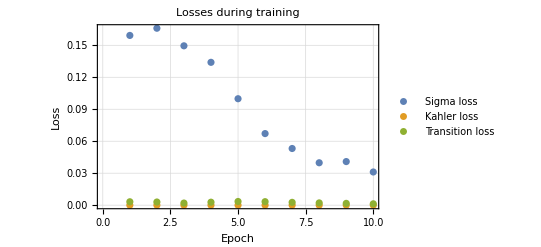

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

```mathematica
history[["transition_val"]]
```

{0.00316606,0.002591,0.00197475,0.00274067,0.00348064,0.00330943,0.0027071,0.00217046,0.00166029,0.00126955}

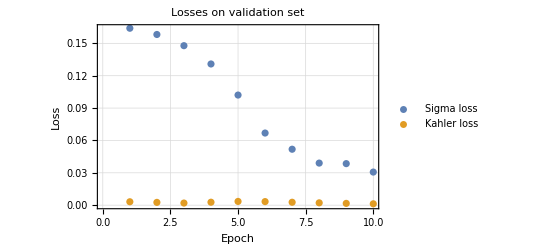

```mathematica
ListPlot[{history[["sigma_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

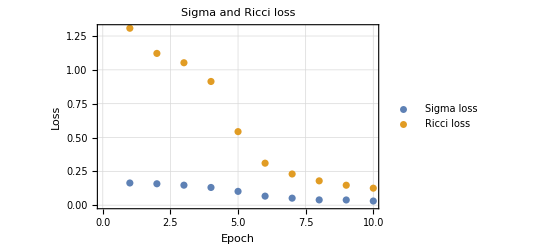

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",FrameLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

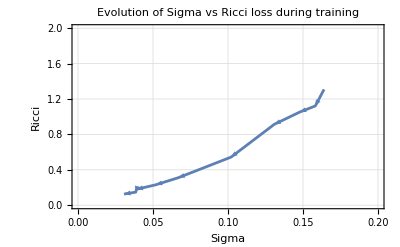

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",FrameLabel->{"Sigma","Ricci"},PlotRange->{{0,0.2},{0,2}},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

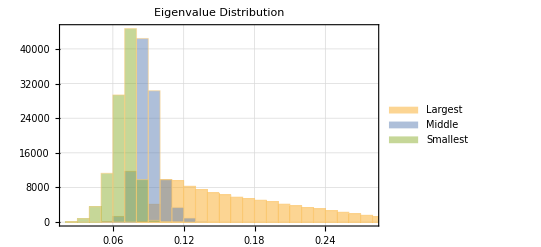

```mathematica
EigVals=Table[Eigenvalues[metrics[[i]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```